## 250412 (Pt, inside farady box) _001_002

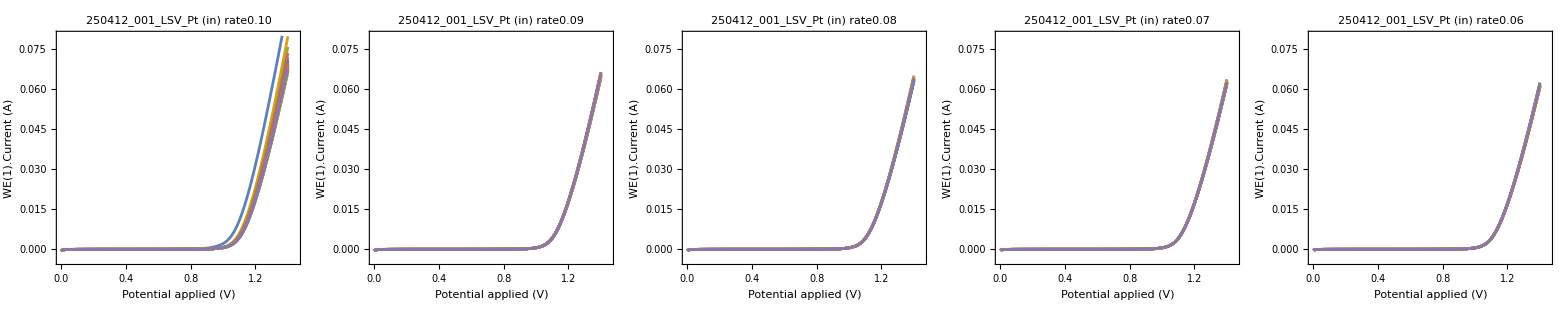

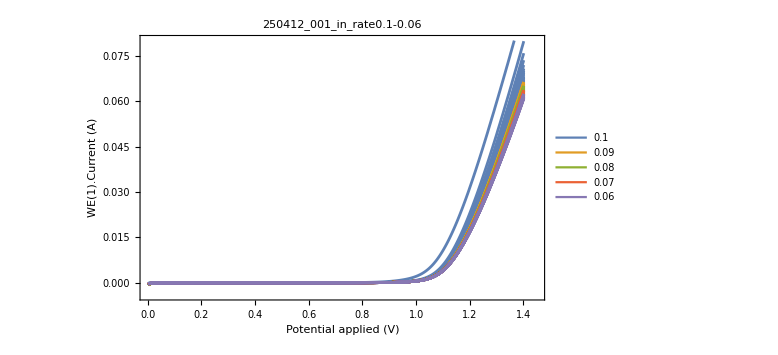

```mathematica
baseDir="C:\\Users\\kelvi\\OneDrive\\桌面\\Data\\250412_001_LSV_Pt";
rateList=Range[0.10,0.06,-0.01];
rateFolders=FileNameJoin[{baseDir,"rate"<>ToString[NumberForm[#,{3,2}]]}]&/@rateList;
rateDataSets=Table[Module[{files,data},files=FileNameJoin[{folder,ToString[#]}]&/@Range[1,20];
data=Import[#,"Table","HeaderLines"->3,"FieldSeparators"->"\t"]&/@files;
data=Module[{d=#},If[MatrixQ[d]&&Depth[d]==3,d,Transpose[d]]]&/@data;
data],{folder,rateFolders}];


(*產生圖，每個 rate 一張圖*)
plots=Table[ListLinePlot[rateDataSets[[i]],PlotRange->{{0,1.45},{-0.004,0.08}},PlotStyle->ColorData[97,"ColorList"],Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLabel->FileNameTake[baseDir,-1]<>" (in) "<>FileNameTake[rateFolders[[i]],-1],ImageSize->300],{i,Length[rateFolders]}];
TableForm[{plots}]

(*合併所有曲線資料成一個 list，同時建立對應顏色表*)
allCurves=Flatten[rateDataSets,1];
colors=ColorData[97,"ColorList"][[1;;Length[rateList]]];
plotColors=Flatten[Table[ConstantArray[colors[[i]],20],{i,Length[rateList]}]];
ListLinePlot[allCurves,PlotRange->{{0,1.45},{-0.004,0.08}},PlotStyle->plotColors,Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLegends->Placed[LineLegend[colors,ToString/@rateList],Right],PlotLabel->"250412_001_in_rate0.1-0.06",ImageSize->Large]
```

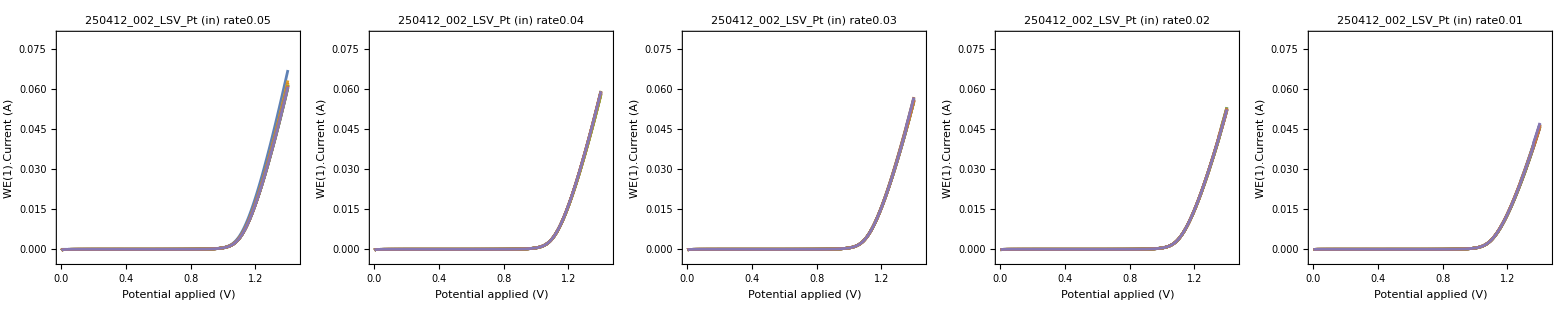

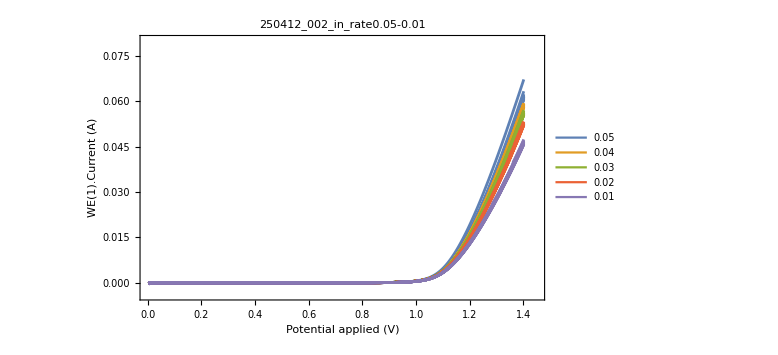

```mathematica
baseDir="C:\\Users\\kelvi\\OneDrive\\桌面\\Data\\250412_002_LSV_Pt";
rateList=Range[0.05,0.01,-0.01];
rateFolders=FileNameJoin[{baseDir,"rate"<>ToString[NumberForm[#,{3,2}]]}]&/@rateList;
rateDataSets=Table[Module[{files,data},files=FileNameJoin[{folder,ToString[#]}]&/@Range[1,20];
data=Import[#,"Table","HeaderLines"->3,"FieldSeparators"->"\t"]&/@files;
data=Module[{d=#},If[MatrixQ[d]&&Depth[d]==3,d,Transpose[d]]]&/@data;
data],{folder,rateFolders}];


plots=Table[ListLinePlot[rateDataSets[[i]],PlotRange->{{0,1.45},{-0.004,0.08}},PlotStyle->ColorData[97,"ColorList"],Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLabel->FileNameTake[baseDir,-1]<>" (in) "<>FileNameTake[rateFolders[[i]],-1],ImageSize->300],{i,Length[rateFolders]}];
TableForm[{plots}]


allCurves=Flatten[rateDataSets,1];
colors=ColorData[97,"ColorList"][[1;;Length[rateList]]];
plotColors=Flatten[Table[ConstantArray[colors[[i]],20],{i,Length[rateList]}]];
ListLinePlot[allCurves,PlotRange->{{0,1.45},{-0.004,0.08}},PlotStyle->plotColors,Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLegends->Placed[LineLegend[colors,ToString/@rateList],Right],PlotLabel->"250412_002_in_rate0.05-0.01",ImageSize->Large]
```

## 250412 (Pt, outside farady box) _003

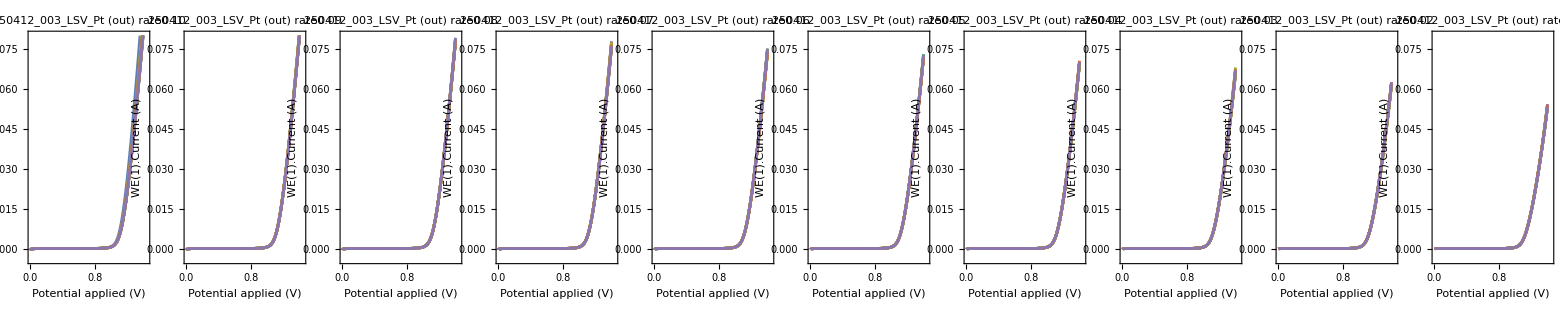

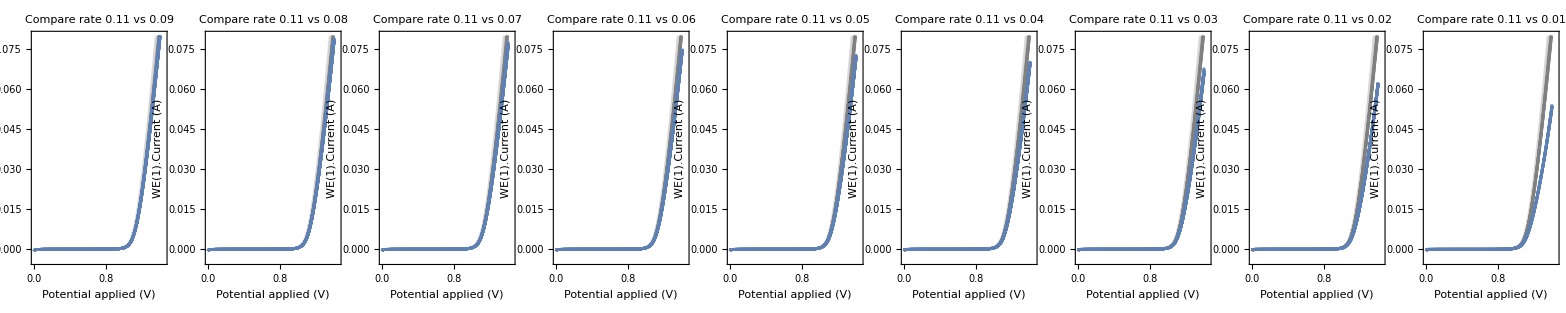

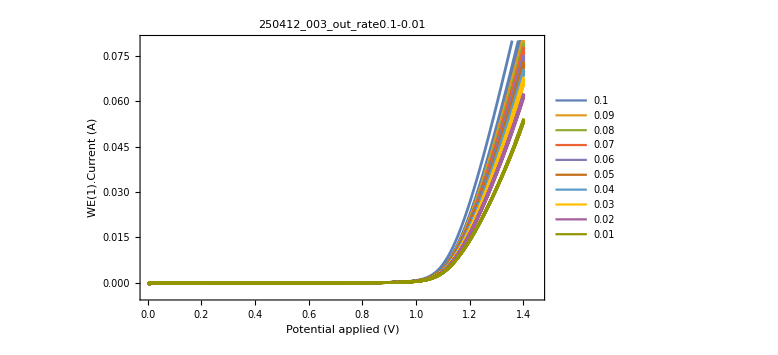

```mathematica
baseDir="C:\\Users\\kelvi\\OneDrive\\桌面\\Data\\250412_003_LSV_Pt";
rateList=Range[0.10,0.01,-0.01];
rateFolders=FileNameJoin[{baseDir,"rate"<>ToString[NumberForm[#,{3,2}]]}]&/@rateList;
rateDataSets=Table[Module[{files,data},files=FileNameJoin[{folder,ToString[#]}]&/@Range[1,20];
data=Import[#,"Table","HeaderLines"->3,"FieldSeparators"->"\t"]&/@files;
data=Module[{d=#},If[MatrixQ[d]&&Depth[d]==3,d,Transpose[d]]]&/@data;
data],{folder,rateFolders}];

(*產生圖，每個 rate 一張圖*)
plots=Table[ListLinePlot[rateDataSets[[i]],PlotRange->{{0,1.45},{-0.004,0.08}},PlotStyle->ColorData[97,"ColorList"],Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLabel->FileNameTake[baseDir,-1]<>" (out) "<>FileNameTake[rateFolders[[i]],-1],ImageSize->300],{i,Length[rateFolders]}];
TableForm[{plots}]

(*比較 baseline(0.01) vs 每一個其他 rate，每個圖 20 條+20 條線，共 40 條*)
baselineData=rateDataSets[[1]];
baselineColor=Directive[Gray, Opacity[0.3]];
comparisonPlots=Table[Module[{testData=rateDataSets[[i]]},If[Length[testData]==20,ListLinePlot[Join[Table[Style[baselineData[[j]],baselineColor],{j,1,20}],Table[Style[testData[[j]],colors[[1]]],{j,1,20}]],PlotRange->{{0,1.45},{-0.004,0.08}},Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLabel->"Compare rate 0.11 vs "<>ToString[rateList[[i]]],ImageSize->300],Style["Data missing for rate "<>ToString[rateList[[i]]],Red]]],{i,2,Length[rateList]}];
TableForm[{comparisonPlots}]

(*合併所有曲線資料成一個 list，同時建立對應顏色表*)
allCurves=Flatten[rateDataSets,1];
colors=ColorData[97,"ColorList"][[1;;Length[rateList]]];
plotColors=Flatten[Table[ConstantArray[colors[[i]],20],{i,Length[rateList]}]];
ListLinePlot[allCurves,PlotRange->{{0,1.45},{-0.004,0.08}},PlotStyle->plotColors,Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLegends->Placed[LineLegend[colors,ToString/@rateList],Right],PlotLabel->"250412_003_out_rate0.1-0.01",ImageSize->Large]
```

## 250414 (Pt, outside farady box) _001

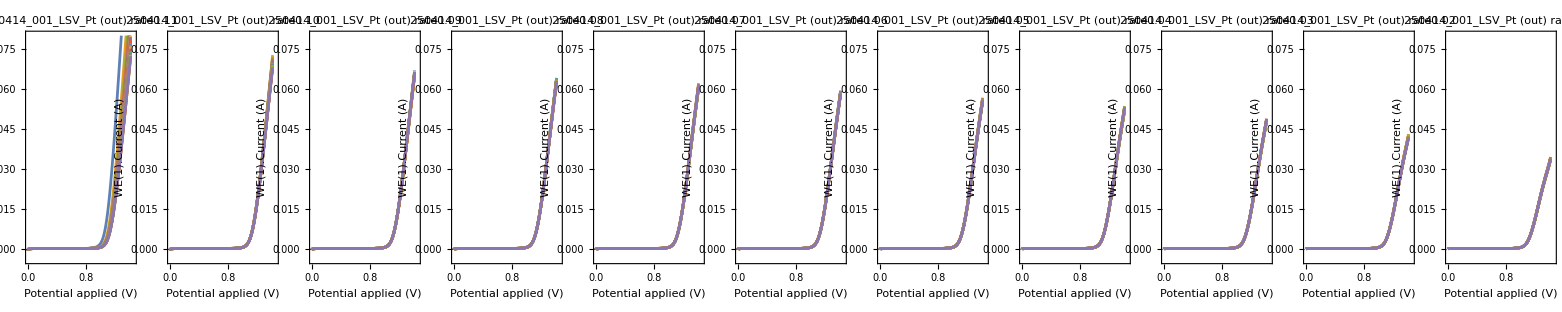

-Graphics-

-Graphics-

```mathematica
baseDir="C:\\Users\\kelvi\\OneDrive\\桌面\\Data\\250414_001_LSV_Pt";
rateList=Range[0.11,0.01,-0.01];
rateFolders=FileNameJoin[{baseDir,"rate"<>ToString[NumberForm[#,{3,2}]]}]&/@rateList;
rateDataSets=Table[Module[{files,data},files=FileNameJoin[{folder,ToString[#]}]&/@Range[1,20];
data=Import[#,"Table","HeaderLines"->4,"FieldSeparators"->"\t"]&/@files;
data=Module[{d=#},If[MatrixQ[d]&&Depth[d]==3,d,Transpose[d]]]&/@data;
data],{folder,rateFolders}];


plots=Table[ListLinePlot[rateDataSets[[i]],PlotRange->{{0,1.45},{-0.004,0.08}},PlotStyle->ColorData[97,"ColorList"],Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLabel->FileNameTake[baseDir,-1]<>" (out) "<>FileNameTake[rateFolders[[i]],-1],ImageSize->300],{i,Length[rateFolders]}];
TableForm[{plots}]

(*比較 baseline(0.01) vs 每一個其他 rate，每個圖 20 條+20 條線，共 40 條*)
baselineData=rateDataSets[[1]]; 
baselineColor=Directive[Gray,Opacity[0.3]];
comparisonPlots=Table[Module[{testData=rateDataSets[[i]]},If[Length[testData]==20,ListLinePlot[Join[Table[Style[baselineData[[j]],baselineColor],{j,1,20}],Table[Style[testData[[j]],colors[[1]]],{j,1,20}]],PlotRange->{{0,1.45},{-0.004,0.08}},Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLabel->"Compare rate 0.11 vs "<>ToString[rateList[[i]]],ImageSize->300],Style["Data missing for rate "<>ToString[rateList[[i]]],Red]]],{i,2,Length[rateList]}];
TableForm[{comparisonPlots}]


allCurves=Flatten[rateDataSets,1];
colors=ColorData[97,"ColorList"][[1;;Length[rateList]]];
plotColors=Flatten[Table[ConstantArray[colors[[i]],20],{i,Length[rateList]}]];
ListLinePlot[allCurves,PlotRange->{{0,1.45},{-0.004,0.08}},PlotStyle->plotColors,Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLegends->Placed[LineLegend[colors,ToString/@rateList],Right],PlotLabel->"250414_001_out_rate0.1-0.01",ImageSize->Large]
```

## 250414 (Pt, inside farady box) _002

```mathematica
baseDir="C:\\Users\\kelvi\\OneDrive\\桌面\\Data\\250414_002_LSV_Pt";
rateList=Range[0.11,0.01,-0.01];
rateFolders=FileNameJoin[{baseDir,"rate"<>ToString[NumberForm[#,{3,2}]]}]&/@rateList;
(*將每個 folder 中的 1–20 號檔案轉為資料矩陣*)
rateDataSets=Table[Module[{files,data},files=FileNameJoin[{folder,ToString[#]}]&/@Range[1,20];
data=Import[#,"Table","HeaderLines"->4,"FieldSeparators"->"\t"]&/@files;
(*確保每筆資料為二維 {x,y} 格式*)
data=Module[{d=#},If[MatrixQ[d]&&Depth[d]==3,d,Transpose[d]]]&/@data;
data],{folder,rateFolders}];

(*產生圖，每個 rate 一張圖*)
plots=Table[ListLinePlot[rateDataSets[[i]],PlotRange->{{0,1.45},{-0.004,0.08}},PlotStyle->ColorData[97,"ColorList"],Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLabel->FileNameTake[baseDir,-1]<>" (in) "<>FileNameTake[rateFolders[[i]],-1],ImageSize->300],{i,Length[rateFolders]}];
TableForm[{plots}]

(*比較 baseline vs 每一個其他 rate，每個圖 20 條+20 條線，共 40 條*)
baselineData=rateDataSets[[1]]; (*提取rate0.11 當 baseline*)
baselineColor=Directive[Gray,Opacity[0.3]];
comparisonPlots=Table[Module[{testData=rateDataSets[[i]]},If[Length[testData]==20,ListLinePlot[Join[Table[Style[baselineData[[j]],baselineColor],{j,1,20}],Table[Style[testData[[j]],colors[[1]]],{j,1,20}]],PlotRange->{{0,1.45},{-0.004,0.08}},Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLabel->"Compare rate 0.11 vs "<>ToString[rateList[[i]]],ImageSize->300],Style["Data missing for rate "<>ToString[rateList[[i]]],Red]]],{i,2,Length[rateList]}];
TableForm[{comparisonPlots}]


(*合併所有曲線資料成一個 list，同時建立對應顏色表*)
allCurves=Flatten[rateDataSets,1];
colors=ColorData[97,"ColorList"][[1;;Length[rateList]]];
plotColors=Flatten[Table[ConstantArray[colors[[i]],20],{i,Length[rateList]}]];
ListLinePlot[allCurves,PlotRange->{{0,1.45},{-0.004,0.08}},PlotStyle->plotColors,Frame->True,FrameLabel->{"Potential applied (V)","WE(1).Current (A)"},PlotLegends->Placed[LineLegend[colors,ToString/@rateList],Right],PlotLabel->"250414_002_in_rate0.1-0.01",ImageSize->Large]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

-Graphics-